## Band adjuster - Lu163

### The fit for modified TSD4

## The 4th band is adjusted such that the theoretical values reproduce the experimental

```mathematica
TSD4={{23.5,4.58},{25.5,5.2251},{27.5,5.9273},{29.5,6.6819},{31.5,7.4919},{33.5,8.3573},{35.5,9.2778},{37.5,10.2535},{39.5,11.2851},{41.5,12.3701}};
TSD4Th={{23.5,4.35287},{25.5,5.14738},{27.5,6.01498},{29.5,6.9558},{31.5,7.96994},{33.5,9.05748},{35.5,10.2185},{37.5,11.4531},{39.5,12.7612},{41.5,14.1429}};
Delta=Table[TSD4Th[[i,2]]-TSD4[[i,2]],{i,1,Length[TSD4]}];
```

```mathematica
#[[2]]&/@TSD4
```

{4.58,5.2251,5.9273,6.6819,7.4919,8.3573,9.2778,10.2535,11.2851,12.3701}

## the adjuster function (create table for modified experimental values based on the ThData and the Deltas)

```mathematica
TSD4Adjusted[SOURCE_,adjuster_]:=Table[{SOURCE[[i,1]],SOURCE[[i,2]]-adjuster[[i]]},{i,1,Length[SOURCE]}];
```

## graphical representation of the adjuster method

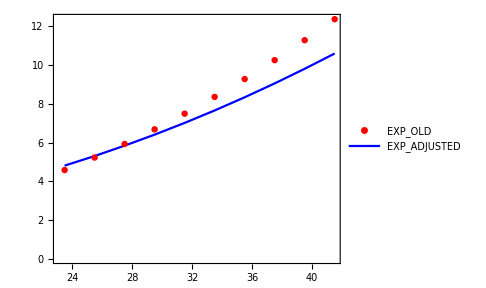

```mathematica
ListPlot[{TSD4,TSD4Adjusted[TSD4,Delta]},PlotStyle->{Red,Blue},Frame->True,Axes->False,Joined->{False, True},PlotLegends->{"EXP_OLD","EXP_ADJUSTED"},ImageSize->Medium,AspectRatio->0.8]
```

## The adjusted experimental data set (to be used in the fitting procedure)

### Fitting the experimental energies - experimental data for the other three bands

```mathematica
TSD1={{8.5,0.1966},{10.5,0.4597},{12.5,0.7746},{14.5,1.1609},{16.5,1.6112},{18.5,2.1265},{20.5,2.7051},{22.5,3.3441},{24.5,4.0411},{26.5,4.7937},{28.5,5.5992},{30.5,6.457},{32.5,7.3667},{34.5,8.3293},{36.5,9.3458},{38.5,10.4169},{40.5,11.5431},{42.5,12.7224},{44.5,13.9491},{46.5,15.2181},{48.5,16.5221}};
TSD2={{13.5,1.3394},{15.5,1.7467},{17.5,2.2184},{19.5,2.7527},{21.5,3.3484},{23.5,4.003},{25.5,4.7143},{27.5,5.4805},{29.5,6.3004},{31.5,7.1733},{33.5,8.0998},{35.5,9.08},{37.5,10.1147},{39.5,11.2036},{41.5,12.3466},{43.5,13.5441},{45.5,14.7911}};
TSD3={{16.5,2.1237},{18.5,2.6293},{20.5,3.1973},{22.5,3.8243},{24.5,4.5094},{26.5,5.2506},{28.5,6.0465},{30.5,6.8963},{32.5,7.7988},{34.5,8.7546},{36.5,9.7638},{38.5,10.8268},{40.5,11.9392},{42.5,13.0861}};
(*TSD4={{23.5,4.58},{25.5,5.2251},{27.5,5.9273},{29.5,6.6819},{31.5,7.4919},{33.5,8.3573},{35.5,9.2778},{37.5,10.2535},{39.5,11.2851},{41.5,12.3701}};*)
```

```mathematica
TSD4New=TSD4Adjusted[TSD4,Delta];
```

```mathematica
spins=Join[Table[TSD1[[i,1]],{i,1,Length[TSD1]}],Table[TSD2[[i,1]],{i,1,Length[TSD2]}],Table[TSD3[[i,1]],{i,1,Length[TSD3]}],Table[TSD4New[[i,1]],{i,1,Length[TSD4New]}]];
ExperimentalEnergies=Join[Table[TSD1[[i,2]],{i,1,Length[TSD1]}],Table[TSD2[[i,2]],{i,1,Length[TSD2]}],Table[TSD3[[i,2]],{i,1,Length[TSD3]}],Table[TSD4New[[i,2]],{i,1,Length[TSD4New]}]];
```

```mathematica
TSD4New
```

{{23.5,4.80713},{25.5,5.30282},{27.5,5.83962},{29.5,6.408},{31.5,7.01386},{33.5,7.65712},{35.5,8.3371},{37.5,9.0539},{39.5,9.809},{41.5,10.5973}}

## Formulas

```mathematica
moi[k_,i0_,γ_,β_]:=i0/(1+(5/(16π))^(1/2)*β)*(1-(5/(4π))^(1/2)β*Cos[γ*π/180+2/3 π*k]);
a1[i0_,γ_,β_]:=1/(2*moi[1,i0,γ,β]);
a2[i0_,γ_,β_]:=1/(2*moi[2,i0,γ,β]);
a3[i0_,γ_,β_]:=1/(2*moi[3,i0,γ,β]);
```

```mathematica
hMin[spin_,oddSpin_,i0_,v_,γ_,β_]:=(a2[i0,γ,β]+a3[i0,γ,β])*(spin+oddSpin)/2+a1[i0,γ,β]*(spin-oddSpin)^2-v*(2oddSpin-1)/(oddSpin+1)*Sin[γ*π/180+π/6];
b1[spin_,oddSpin_,i0_,v_,γ_,β_]:=-1*(((2spin-1)(a3[i0,γ,β]-a1[i0,γ,β])+2oddSpin*a1[i0,γ,β])((2spin-1)(a2[i0,γ,β]-a1[i0,γ,β])+2*oddSpin*a1[i0,γ,β])+8spin*oddSpin*a2[i0,γ,β]*a3[i0,γ,β]+((2oddSpin-1)*(a3[i0,γ,β]-a1[i0,γ,β])+2spin*a1[i0,γ,β]+v*(2oddSpin-1)/(oddSpin(oddSpin+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))*((2oddSpin-1)*(a2[i0,γ,β]-a1[i0,γ,β])+2spin*a1[i0,γ,β]+v*(2oddSpin-1)/(oddSpin(oddSpin+1))2 √3 Sin[γ*π/180]));
c1[spin_,oddSpin_,i0_,v_,γ_,β_]:=(((2spin-1)*(a3[i0,γ,β]-a1[i0,γ,β])+2oddSpin*a1[i0,γ,β])*((2oddSpin-1)*(a3[i0,γ,β]-a1[i0,γ,β])+2spin*a1[i0,γ,β]+v*(2oddSpin-1)/(oddSpin(oddSpin+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))-4spin*oddSpin*a3[i0,γ,β]^2)*(((2spin-1)*(a2[i0,γ,β]-a1[i0,γ,β])+2oddSpin*a1[i0,γ,β])*((2oddSpin-1)(a2[i0,γ,β]-a1[i0,γ,β])+2*spin*a1[i0,γ,β]+v*(2oddSpin-1)/(oddSpin*(oddSpin+1))2 √3 Sin[γ*π/180])-4spin*oddSpin*a2[i0,γ,β]^2);
Omega1[spin_,oddSpin_,i0_,v_,γ_,β_]:=√(1/2(-b1[spin,oddSpin,i0,v,γ,β]+(b1[spin,oddSpin,i0,v,γ,β]^2-4c1[spin,oddSpin,i0,v,γ,β])^(1/2)));
Omega2[spin_,oddSpin_,i0_,v_,γ_,β_]:=√(1/2(-b1[spin,oddSpin,i0,v,γ,β]-(b1[spin,oddSpin,i0,v,γ,β]^2-4c1[spin,oddSpin,i0,v,γ,β])^(1/2)));
```

```mathematica
energyExpression[n1_,n2_,spin_,oddSpin_,i0_,v_,γ_,β_]:=hMin[spin,oddSpin,i0,v,γ,β]+Omega1[spin,oddSpin,i0,v,γ,β]*(n1+1/2)+Omega2[spin,oddSpin,i0,v,γ,β]*(n2+1/2);
e0[i0_,v_,γ_,β_]:=energyExpression[0,0,6.5,6.5,i0,v,γ,β];
energyTSD1[spin_,i0_,v_,γ_,β_]:=If[Im[energyExpression[0,0,spin,6.5,i0,v,γ,β]-e0[i0,v,γ,β]]==0,energyExpression[0,0,spin,6.5,i0,v,γ,β]-e0[i0,v,γ,β],10^11];
energyTSD2[spin_,i0_,v_,γ_,β_]:=If[Im[energyExpression[1,0,spin-1,6.5,i0,v,γ,β]-e0[i0,v,γ,β]]==0,energyExpression[1,0,spin-1,6.5,i0,v,γ,β]-e0[i0,v,γ,β],10^11];
energyTSD3[spin_,i0_,v_,γ_,β_]:=If[Im[energyExpression[2,0,spin-2,6.5,i0,v,γ,β]-e0[i0,v,γ,β]]==0,energyExpression[2,0,spin-2,6.5,i0,v,γ,β]-e0[i0,v,γ,β],10^11];
energyTSD4[spin_,i0_,v_,γ_,β_]:=If[Im[energyExpression[3,0,spin-3,4.5,i0,v,γ,β]-e0[i0,v,γ,β]]==0,energyExpression[3,0,spin-3,4.5,i0,v,γ,β]-e0[i0,v,γ,β],10^11];
```

## RMS fit

```mathematica
RMS[expdata_,thdata_]:=√(Sum[(expdata[[i]]-thdata[[i]])^2,{i,1,Length[expdata]}]/(Length[expdata]-1));
```

## deformation parameters

```mathematica
deformationParameters={17,0.38};
```

## joint data

```mathematica
dataX=Join[Insert[#,1,1]&/@TSD1,Insert[#,2,1]&/@TSD2,Insert[#,3,1]&/@TSD3,Insert[#,4,1]&/@TSD4New];
```

```mathematica
dataX
```

{{1,8.5,0.1966},{1,10.5,0.4597},{1,12.5,0.7746},{1,14.5,1.1609},{1,16.5,1.6112},{1,18.5,2.1265},{1,20.5,2.7051},{1,22.5,3.3441},{1,24.5,4.0411},{1,26.5,4.7937},{1,28.5,5.5992},{1,30.5,6.457},{1,32.5,7.3667},{1,34.5,8.3293},{1,36.5,9.3458},{1,38.5,10.4169},{1,40.5,11.5431},{1,42.5,12.7224},{1,44.5,13.9491},{1,46.5,15.2181},{1,48.5,16.5221},{2,13.5,1.3394},{2,15.5,1.7467},{2,17.5,2.2184},{2,19.5,2.7527},{2,21.5,3.3484},{2,23.5,4.003},{2,25.5,4.7143},{2,27.5,5.4805},{2,29.5,6.3004},{2,31.5,7.1733},{2,33.5,8.0998},{2,35.5,9.08},{2,37.5,10.1147},{2,39.5,11.2036},{2,41.5,12.3466},{2,43.5,13.5441},{2,45.5,14.7911},{3,16.5,2.1237},{3,18.5,2.6293},{3,20.5,3.1973},{3,22.5,3.8243},{3,24.5,4.5094},{3,26.5,5.2506},{3,28.5,6.0465},{3,30.5,6.8963},{3,32.5,7.7988},{3,34.5,8.7546},{3,36.5,9.7638},{3,38.5,10.8268},{3,40.5,11.9392},{3,42.5,13.0861},{4,23.5,4.80713},{4,25.5,5.30282},{4,27.5,5.83962},{4,29.5,6.408},{4,31.5,7.01386},{4,33.5,7.65712},{4,35.5,8.3371},{4,37.5,9.0539},{4,39.5,9.809},{4,41.5,10.5973}}

## Fit - all values

```mathematica
(*nlm=NonlinearModelFit[dataX,{Boole[id==1]*energyTSD1[x,a,b,deformationParameters[[1]],deformationParameters[[2]]]+Boole[id==2]*energyTSD2[x,a,b,deformationParameters[[1]],deformationParameters[[2]]]+Boole[id==3]*energyTSD3[x,a,b,deformationParameters[[1]],deformationParameters[[2]]]+Boole[id==4]*energyTSD4[x,a,b,deformationParameters[[1]],deformationParameters[[2]]]},{a,b},{id,x}];
bestParams=nlm["BestFitParameters"];*)
```

```mathematica
bestParams={51.59,0.0601};
```

```mathematica
TSD1Th=Table[{TSD1[[i,1]],energyTSD1[TSD1[[i,1]],bestParams[[1]],bestParams[[2]],deformationParameters[[1]],deformationParameters[[2]]]},{i,1,Length[TSD1]}];
TSD2Th=Table[{TSD2[[i,1]],energyTSD2[TSD2[[i,1]],bestParams[[1]],bestParams[[2]],deformationParameters[[1]],deformationParameters[[2]]]},{i,1,Length[TSD2]}];
TSD3Th=Table[{TSD3[[i,1]],energyTSD3[TSD3[[i,1]],bestParams[[1]],bestParams[[2]],deformationParameters[[1]],deformationParameters[[2]]]},{i,1,Length[TSD3]}];
TSD4ThAdjusted=Table[{TSD4[[i,1]],energyTSD4[TSD4[[i,1]],bestParams[[1]],bestParams[[2]],deformationParameters[[1]],deformationParameters[[2]]]},{i,1,Length[TSD4]}];
```

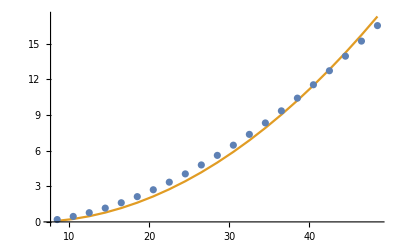

```mathematica
ListPlot[{TSD1,TSD1Th},Joined->{False, True}]
```

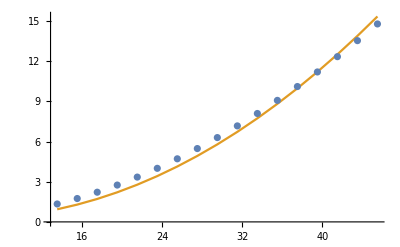

```mathematica
ListPlot[{TSD2,TSD2Th},Joined->{False, True}]
```

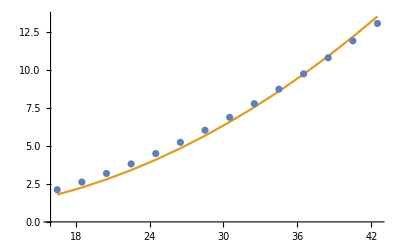

```mathematica
ListPlot[{TSD3,TSD3Th},Joined->{False, True}]
```

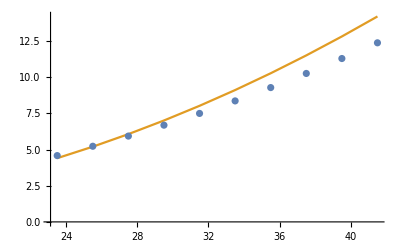

```mathematica
ListPlot[{TSD4,TSD4ThAdjusted},Joined->{False, True}]
```

```mathematica
TSD4ThAdjusted
```

{{23.5,4.40075},{25.5,5.19562},{27.5,6.06346},{29.5,7.00441},{31.5,8.01859},{33.5,9.10607},{35.5,10.267},{37.5,11.5013},{39.5,12.8091},{41.5,14.1905}}